# Empirical Metamathematics: Extending the Lean-to-Mathematica Bridge

## Intro: Why are Lean and Metamath interesting?

From the Project Description: The goal of this project is to do some Metamathematics. The first step will be to work on a Wolfram Language Importer for the Lean Theorem Prover, a currently popular system that blends Interactive and Automated Theorem Proving, two slightly different approaches to finding proofs. Most importantly, Lean draws on the Lean Mathlib collection, made up of thousands of theorems and definitions.

Quick and automated proof checking can help anyone who might like to outsource their proving! Mathematica actually has proving capability and the ProofObject data structure, for equational logic - Lean goes a little further by also allowing quantified terms.

My own way in is that an institute at my university (Research Institute Symbolic Computation at Johannes Kepler University, Linz, Austria) develops a theorem prover that plugs into Mathematica. Bringing in big, community Math theorem packages could be a good way to advance this project. But what is in such a package, how can I explore it? This brings me to Metamathematics and exploring Lean and Mathlib using these approaches.  

However, the focus is a prototype for developing the Lean-to-Mathematica bridge, in case other people are interested in this kind of functionality.

I end on a note about today’s Large Language Models (LLMs) and Neural Networks and how we might plug and play with Metamath, or a metamathematical language, and these new, emergent tools.

```mathematica
(* TODO: Mark, Christopher, Eric, Nik, Mano, Lean Zulip (ok to quote?) WSS2023 *)
```

Attribution:

## Lean-Mathematica Bridge: Setup

The setup part is crucial part of this project: A bridge for Mathematica to talk to Lean (and vice versa) already exists (paper version). As a first step, the WSS project extends (forks) the bridge, to add some convenience functions that can then be used to explore Mathlib, the core, community-driven effort to build a Lean corpus of theorems.

## Bridge Setup

How does the bridge work? The original repository and the fork including the new functionality are on GitHub, but from the Mathematica point of view, we create a Lean-ProcessObject from the externally downloaded executable (see fork-readme for detailed installation instructions).

```mathematica
LeanExecutable = "lean"
```

lean

```mathematica
(* Check/Set the working directory to be mm_lean/src/  *)
```

```mathematica
Directory[]
```

C:\Public\WSS2023\mm-lean\src

```mathematica
SetDirectory["C:\\Public\\WSS2023\\mm-lean\\src"]
```

C:\Public\WSS2023\mm-lean\src

```mathematica
LeanDirectory = "C:\\Public\\WSS2023\\mm-lean\\src"
```

C:\Public\WSS2023\mm-lean\src

```mathematica
(* Import main.m *)
```

```mathematica
<<"main.m";
```

```mathematica
(* Create ProcessObject *)
```

```mathematica
Lean=LeanMode[]
```

ProcessObject[…]

```mathematica
ProcessStatus[Lean]
```

Running

## Mathlib Directory Interface Python Helper-Function

For a note on the semantics of the python program being connected to here, see below section “Meta-Mathematical Explorations of Lean.” (There is a caveat.)

Python was chosen after a brief performance test in comparison to TextSearch[](* //RepeatedTiming *)  in particular. 

To make sure Python is installed and found by Mathematica: FindExternalEvaluators[“Python”] on your system.

```mathematica
MathlibDirectory = "C:\\Public\\WSS2023\\mathlib\\src"
```

C:\Public\WSS2023\mathlib\src

```mathematica
session = StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
TheoremMarker = "(theorem|lemma)" (* Particular to current Lean/Mathlib syntax, see caveat *)
```

(theorem|lemma)

```mathematica
ExternalEvaluate[session, File[LeanDirectory  <>"\\directory_interface.py"]] (* See GitHub *)
```

```mathematica
MathlibTheoremOccurrencesByDomain[domain_] := {domain , ExternalEvaluate[session, <|"Command"->"count_occurrences","Arguments"->{MathlibDirectory <> "\\" <> domain,TheoremMarker}|>] }
```

```mathematica
MathlibDomains = {"algebra","algebraic_geometry","analysis","category_theory","combinatorics","computability","control","data","dynamics","geometry","init","logic","meta","number_theory","order","set_theory","system","tactic","topology"}
```

{algebra,algebraic_geometry,analysis,category_theory,combinatorics,computability,control,data,dynamics,geometry,init,logic,meta,number_theory,order,set_theory,system,tactic,topology}

The above are the domains we will be interested in for the context of this post.

## Lean-Mathematica Bridge: Adding to the Bridge

A quick note on what we are actually doing to begin: we are interfacing with the Lean executable. Under the hood, when call get our additional info about our Lean proof for instance:

```mathematica
GetLeanInfo[p_ProcessObject, name_String] :=
	Module[{res, content},
	       content = StringForm["import main imports set_option pp.beta true open tactic.interactive #view_info ``", name];
	       SendToLeanServer[p, content // ToString];
	       res = HandleLeanServerResponse[p]; ("text" /. res[[1]]) // ToExpression];
```

Getting a (visual, grid) representation works much in the same way: this leads me to finding a way to interpret a proof like this in Mathematica.

## getLeanTree[] to Get a Handle on the Theorems (Make Them Computable)

The main improvement I think I can add to the current bridge is a computable data structure that is also more compact in some ways. Take the following proof grid box as an example:

```mathematica
leanProof = GetLeanProof[Lean,"nat.prime.dvd_of_dvd_pow"]
```

Goal | ∀ {p m n : ℕ}, nat.prime p → p ∣ m ^ n → p ∣ m
ID | 24
Rule | ∀I
Proofs |

Lean is not so much the focus of study here, but this the corresponding Lean code:

theorem prime . dvd_of _dvd _pow {p m n : ℕ} (pp : prime p) (h : p ∣ m^n) : p ∣ m :=
 begin
  induction n with n IH,
  { exact pp . not_dvd _one . elim h },
  { rw pow_succ at h, exact (pp . dvd_mul .1 h) . elim id IH }
end

The statement can be seen as a lemma in number theory. It means that if a prime number p divides m^n (where n is a natural number), then p must divide m.

We can write this as a function too, but it is not a proof, just an application of the theorem (lemma).

```mathematica
PrimeDivisorProp[p_,m_,n_]:=PrimeQ[p]&&Divisible[m^n,p]-> Divisible[m,p]
```

In this function PrimeDivisorProp, we first check if p is prime with PrimeQ[p], then check if p divides m^n with Divisible[m^n, p], and finally we check if p divides m with Divisible[m, p]. The -> operator represents logical implication in Mathematica, which matches the structure of the statement. But again, while this function will correctly express the logical statement, it does not actually prove the statement.

So let’s switch to the Lean bridge: For us it is important to understand that there is some sense in which these proofs unfold from a set of axioms. The project being built on (see introduction) hands out IDs for the individual proof steps.

From the integer ID we can tell that there are 24 theorems involved: this number will come back later. 
But: Even at this size, which could conceivably be a lot bigger, trying to analyse the proof structure quickly becomes unwieldy ...

-Graphics-

A more compact version in the form of a tree structure makes sense, but the built in option still has too much information and is not computable, although the structure is more compact and apparent.

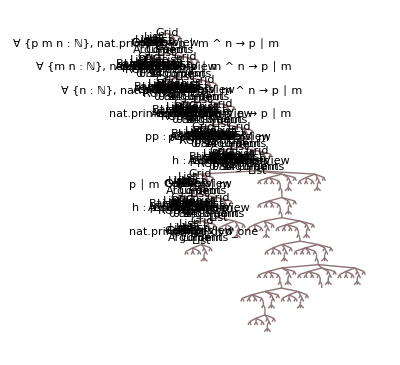

```mathematica
leanProof // TreeForm (* This works quite well in some but not all regards *)
```

So here is a function to simplify to a tree, building on this initial proof representation: The thinking is, this kind of positional structure being interpreted here is liable to be found on some level, although maybe there are better Lean commands to interpret the output of. This shall serve as an initial exploration in this direction, in case this might be something worth further building on.

```mathematica
leanTree = getLeanTree[leanProof] (* In case of memory management issue: ClearAll[getLeanTree] *)
```

-Graphics-

This current iteration maps to the IDs relative to the proof that is being worked out by Lean, but we could also just get Lean syntax representations, or any of the Lean output we are interested in.

The point is that the structure is the proof goal on top, the logical proof steps to get there (proof combinations), starting from the axioms in the leaves. We might want to isolate these, by the way, to see what our basic assumptions (per proof) are.

```mathematica
getLeanAxioms[leanProof]
```

{0,1,2,3,3,3,4,4,5,5,10,10,11,11,14}

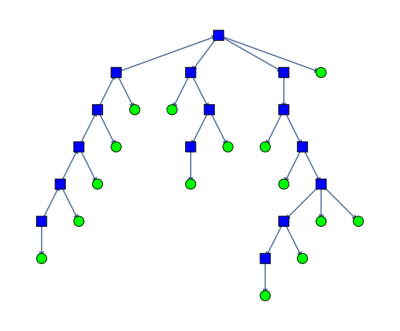

```mathematica
showLeanAxioms[leanProof] (* A TreeGraph visualization test, showing the proportion of leaves to center nodes in a slightly different tree shape *)
```

Or, in case we are just interested in the amount of axioms used, not the structure:

```mathematica
getLeanNumberOfAxioms[leanProof]
```

15

```mathematica
getLeanNumberOfAxiomsUnique[leanProof]
```

9

Let’s move towards more metrics and aways from structure.

## Summary Statistics, or a Metamathematical Language for Proofs?

What the tree representation allows us to do now are simple tree algorithms to get summary statistics concerning the proof set and especially structure of the proof.

```mathematica
leanSize = getLeanSize[leanProof] (* Note that the tree computations happen in the background *)
```

30

We can use the proof grid the original project intended and don’t even need to know about the trees, from the user’s point of view.

```mathematica
highestLeanID = getLeanMaxID[leanProof] (* The tree is used in the background again *)
```

24

Metamathematically interesting to note here: the size of our tree is larger than the largest ID (this is why it makes sense to look at the tree in terms of IDs as well). This is because certain theorems are re-used, so individually there are 24 theorems, but we apply them 30 times. One can think up a utility functions, or better a metric, that might tell us about re-use of theorems, or the re-used theorems.

```mathematica
soWhatLeanMetricExactly = leanSize - highestLeanID (* Tells us the difference between total proofs (or axioms) and unique proofs (or axioms), i.e. how often proof (axioms are re-used) *)
```

6

In this line of thinking: a higher metric would point towards a more repetitive, perhaps more “boring,” proof.

Another simple one: How deep does our tree go?

```mathematica
getLeanDepth[leanProof] (* Tree in the background again *)
```

13

Which might tell us something about how “strenuous,” because of all the steps that occur, or just “deep”, or “involved,” a proof is.

13 is not that deep, by the way: here’s a particularly deep proof!

```mathematica
(* OPTIONAL TUE EVENING TODO 0+: find a deep Mathlib proof *)
```

The focus here has been Lean-Mathematica interoperability and ease of use, by abstracting over the trees which were chosen as the appropriate data structure in the background. Efficiencies might be discovered in that the tree might be easier to construct another way (using more appropriate Lean input), but the idea is to use the tree in the background and keep the original developer’s intentions for proof representations intact. The user needn’t even know about the tree conversion going on in the background.

To make a point about the actual doing of Metamathematics: This is a different approach “under the hood” compared to the directory/web scraping approaches taken in the following, since we are conversing directly with the lean package installed in our system. In the following we will analyse the Mathlib library we specified in setup.

## Meta-Mathematical Explorations of Lean

We continue our exploration on another level, that of our corpus of all proofs, not individual ones (in terms of other proofs and axioms). 
We also make use of a different data structure under the hood: a graph.

## Zoom out: MathLib, Where are We at in 2023?

We have the notion of mathematics as a universal language but we can see here that there is also a body of knowledge (developed by a community) involved. For anyone who might be interested in exploring the metamathematical space: How has this body of knowledge evolved in the past three years, say, and might this indicate something about future development?

The first part to answer this question is from 2020, where I draw on the Euclid article by Stephen Wolfram and others - the focus here was interconnection.

```mathematica
leanAssoc=CloudGet["https://wolfr.am/PL39QRbE"];
```

```mathematica
leanGraph=CloudGet["https://wolfr.am/PL3LfaQ4"];
```

```mathematica
leanDomains = Union[Values[leanAssoc]];
```

```mathematica
leanInfrastructure = {"init", "system", "tactic", "data", "meta", "control", "computability"};
```

```mathematica
leanColors = Merge[{AssociationThread[Complement[leanDomains, leanInfrastructure] -> Take[ColorData[54, "ColorList"], Length[Complement[leanDomains, leanInfrastructure]]]], AssociationThread[leanInfrastructure -> LightGray]}, Identity];
```

```mathematica
leanDomainWeights = Tally[Values[leanAssoc]]
```

{{algebra,8355},{analysis,4021},{geometry,559},{tactic,396},{init,1293},{data,11165},{computability,589},{combinatorics,108},{order,1903},{topology,3220},{logic,483},{category_theory,1834},{number_theory,266},{set_theory,1096},{dynamics,161},{algebraic_geometry,70},{meta,9},{control,161},{system,1}}

```mathematica
leanEdgeWeights = Tally[{leanAssoc[#[[1]]], leanAssoc[#[[2]]]} & /@ EdgeList[leanGraph]];
```

```mathematica
leanEdgesOutSimple = Append[Merge[AssociationThread[{#[[1, 1, 1]]}-> Total[#[[2]]]] & /@ (Transpose /@ GatherBy[Select[leanEdgeWeights, #[[1, 1]] ≠ #[[1, 2]] &], #[[1, 1]] &]), Identity], "init" -> {3493}];
```

```mathematica
leanNormalizedEdgeWeights = DirectedEdge[#[[1, 1]], #[[1, 2]]] -> #[[2]]/ Flatten[leanEdgesOutSimple[#[[1,1]]]] & /@ leanEdgeWeights;
```

```mathematica
diskedLine[{line_,radii_}]:={RegionIntersection[Line[line],Circle[line[[1]],radii[[1]]]][[1,1]],
RegionIntersection[Line[line],Circle[line[[2]],radii[[2]]]][[1,1]]};
```

```mathematica
weightedArrow[line_,weight_]:= Module[{len,start,end,angle, thick, rec, mid},
start=line[[1]]; end=line[[2]]; mid=Mean[line];
len=EuclideanDistance[start,end];
angle=Arg[(start-end).{1,I}];
thick=weight/len;
rec= #+mid&/@(RotationMatrix[angle].#&/@{{-len/2,- thick/2},{len/2,- thick/2},{len/2, thick/2},{-len/2, thick/2}});
Polygon[rec]];
```

```mathematica
VertexDelete[SimpleGraph[Graph[leanDomains, First /@ leanNormalizedEdgeWeights, EdgeStyle->Thread[First/@leanNormalizedEdgeWeights -> ({AbsoluteThickness[20Last[#][[1]]],Arrowheads[Last[#][[1]]/4], GrayLevel[0.5, 0.5]}&/@leanNormalizedEdgeWeights)], VertexSize->Thread[First/@leanDomainWeights -> (Sqrt[#]/90&/@(Last/@leanDomainWeights))], VertexStyle -> (# -> {Lighter /@ leanColors[#]} & /@  leanDomains),  VertexLabels->{"algebra" -> "algebra","algebraic_geometry" -> "algebraic geometry","analysis" -> "analysis","category_theory" -> "category theory","combinatorics" -> "combinatorics","computability" -> "computability","control" -> "control","data" -> "data","dynamics" -> "dynamics","geometry" -> "geometry","init" -> "init","logic" -> "logic","meta" -> "meta","number_theory" -> "number theory","order" -> "order theory","set_theory" -> "set theory","system" -> "system","tactic" -> "tactic","topology" -> "topology"}, GraphLayout -> "SpringElectricalEmbedding", PerformanceGoal->"Quality", AspectRatio->1/4]], {"init", "system", "tactic", "data", "meta", "control", "computability"}, AspectRatio-> 1]
```

-Graphics-

The above emphasizes dependencies and connections, but here we will make our historical comparison simply based on size:

```mathematica
data2020 = leanDomainWeights
```

{{algebra,8355},{analysis,4021},{geometry,559},{tactic,396},{init,1293},{data,11165},{computability,589},{combinatorics,108},{order,1903},{topology,3220},{logic,483},{category_theory,1834},{number_theory,266},{set_theory,1096},{dynamics,161},{algebraic_geometry,70},{meta,9},{control,161},{system,1}}

## Compare to 2023

I want to look at how Mathlib is evolving, particularly what domains are growing the most: We can do this, by “simply” (see caveat below) looking at the structure of the relevant GitHub repository in its current state (July 2023).

```mathematica
data2023 = MathlibTheoremOccurrencesByDomain /@ MathlibDomains
```

{{algebra,10908},{algebraic_geometry,879},{analysis,11486},{category_theory,4575},{combinatorics,1683},{computability,827},{control,198},{data,22410},{dynamics,350},{geometry,1969},{init,0},{logic,1523},{meta,32},{number_theory,1976},{order,7194},{set_theory,2267},{system,0},{tactic,1388},{topology,9398}}

Let’s do some more visualizations.

```mathematica
data2020Clean =Drop[data2020,-2]
```

{{algebra,8355},{analysis,4021},{geometry,559},{tactic,396},{init,1293},{data,11165},{computability,589},{combinatorics,108},{order,1903},{topology,3220},{logic,483},{category_theory,1834},{number_theory,266},{set_theory,1096},{dynamics,161},{algebraic_geometry,70},{meta,9}}

```mathematica
data2023Clean = Drop[data2023,-2]
```

{{algebra,10908},{algebraic_geometry,879},{analysis,11486},{category_theory,4575},{combinatorics,1683},{computability,827},{control,198},{data,22410},{dynamics,350},{geometry,1969},{init,0},{logic,1523},{meta,32},{number_theory,1976},{order,7194},{set_theory,2267},{system,0}}

## Caveat

This data comes about through web/directory scraping, some time around 2020 when the article was published. But Mathlib evolves and in fact is becoming very big. Asking about this in the Lean Zulip forum, Scott Morrison, one of the programmers and mathematicians working on Lean, responds: “Overall, I would say Mathlib is already too big to “get a sense of all the theorems” in any meaningful [way]! I’m sure every expert here is regularly surprised to find that something is, or is not, in the library. (Within specific areas this is not true.)” And: “The directory structure in Mathlib is fairly ad-hoc and to a large extent based on historical accident, so be very skeptical of any ‘overview’ based on analyzing file names or namespaces!”

## Zoom Back In: Theorems Crossing Domains, More Metamathematical Language for Theorems

Back on the level of individual theorems we might like to make visible the area of mathematics they originate from and how they can come together for different kinds of proofs. (This shows one way different levels of abstraction in metamathematics can work.) This may even allow us to articulate metamathematical statements about proofs, maybe saying something about how “surprising,” or “encompassing” a given proof is.

```mathematica
(* TUE EVENING TODO: python tool to get category name from given theorem, how to package in a function? Taking this further, can we do this for all the theorems in a proof, i.e. giving all the categories a theorem "crosses"? *)
```

## Possible Broader Implications

As a side-note about potential implications, with LLMs recent rise to prominence, this kind of metamathematical language (word choices) as well as metamathematical programming languages like Lean might be particularly fruitful. One can imagine Neural Networks exploring these metamathematical theorem spaces in ways approaching how humans do mathematics: But I defer to Stephen Wolfram on the details of the broader implications and this line of thinking, outside of the scope of this project for now.

## Instantiations, Limitations

Some of these functions are still being developed (see in repo), and maybe the assumptions are not correct: There are almost certainly better ways to get to a Lean response, but the hope is that similar kinds of structural analysis as are used here would be needed. Finally, this author’s own current limitation is his level of Lean learning, which would need to improve to go in this direction further.